# Primordial Gravitational Waves in Modified Gravity

```mathematica
ClearAll["Global`*"];
SetDirectory[FileNameJoin[ {NotebookDirectory[],"data"}]];
preventSave=False;
```

## Constants

```mathematica
h0 = 0.72;
H0 = 100*h0/300000;(*Quantity["km/(Mpc*s)"]*)
ωb0=0.02264;
ωm0=0.1138;
```

### Matter densities

```mathematica
Ωb[a_]:=ωb0/h0^2*a^-3(* baryonic matter *)
Ωm[a_]:=ωm0/h0^2*a^-3(* dark matter *)
Ωv[a_]:=1-((ωb0+ωm0)/h0^2)(* dark energy *)
{Ωb[1],Ωm[1],Ωv[1]}*100
```

{4.36728,21.9522,73.6806}

### Hubble function

```mathematica
H[x_]:=H0*Sqrt[Ωb[a]+Ωm[a]+Ωv[a]]/.a->Exp[x];
Hconf[x_]:=H[x]*Exp[x];
```

## Amplitude of the perturbation

```mathematica
r=0.05;
k0=0.05;
AS=Exp[3.089442]*10^-10;
AT=r*AS;
nT=-r/8;
hA[k_]=Sqrt[AT*(k/k0)^nT];(* Amplitude *)
```

## Solution for constant αM

```mathematica
aInitial=10^-10;
sol=ParametricNDSolve[{h''[x]+(Hconf'[x]/Hconf[x]+2+αM)*h'[x]+(cT*k/Hconf[x])^2*h[x]==0,h[Log[aInitial]]==1,h'[Log[aInitial]]==0},h,{x,Log[aInitial],0},{k,cT,αM}];
ha[k_,cT_,αM_][a_]=hA[k]*h[k,cT,αM][x]/.sol/.x->Log[a];
Options[makePlot]={SaveFilePrefix->Null};
makePlot[h_,pvalues_,OptionsPattern[]]:=(
param=pvalues[[1]];
plabel=ToString[param];
If[Not[OptionValue[SaveFilePrefix]===Null]&&Not[preventSave],
Do[
data =Table[{x,Log10[Abs[h[10^x]]]},{x,-5,0,0.001}];
Export[OptionValue[SaveFilePrefix]<>"_"<>TextString[param]<>".csv",data];
,pvalues];
];
LogLogPlot[Evaluate[Table[Abs[h[a]],pvalues]],{a,10^-5,1},PlotLegends->Placed[Table[plabel<>"="<>TextString[param],pvalues],Right]]
)
```

### Varying αM

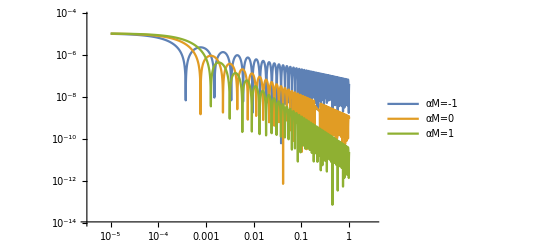

```mathematica
makePlot[ha[0.01,1,αM],{αM,-1,1,1},SaveFilePrefix->"varying_aM"]
```

Increasing αM introduces more friction, so the amplitude of the gravitational wave decreases more rapidly.

### Varying k

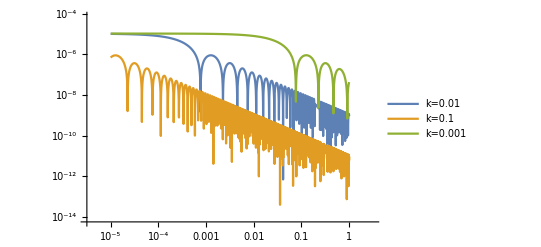

```mathematica
makePlot[ha[k,1,0],{k,{0.01,0.1,0.001}},SaveFilePrefix->"varying_k"]
```

The gravitational wave enters the horizon earlier for larger modes k.

### Varying cT

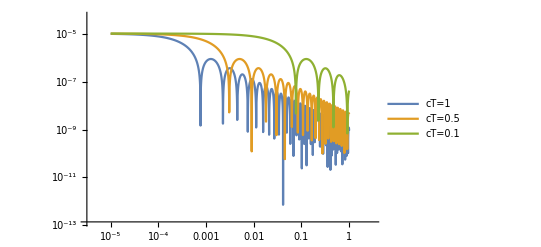

```mathematica
makePlot[ha[0.01,cT,0],{cT,{1,0.5,0.1}},SaveFilePrefix->"varying_cT"]
```

For a slower propagation, the wave enters the horizon later.

## Solution for parametrized αM

```mathematica
αM[αM0_,β_][x_]:=αM0*Exp[x*β];
aInitial=10^-10;
sol=ParametricNDSolve[{h''[x]+(Hconf'[x]/Hconf[x]+2+αM[αM0,β][x])*h'[x]+(cT*k/Hconf[x])^2*h[x]==0,h[Log[aInitial]]==1,h'[Log[aInitial]]==0},h,{x,Log[aInitial],0},{αM0,β,cT,k}];
haβ[αM0_,β_,cT_,k_][a_]=hA[k]*h[αM0,β,cT,k][x]/.sol/.x->Log[a];
```

### Varying β

#### αM0=-1

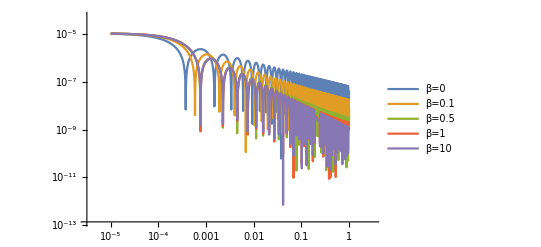

```mathematica
makePlot[haβ[-1,β,1,0.01],{β,{0,0.1,0.5,1,10}},SaveFilePrefix->"varying_beta"]
```

#### αM0=1

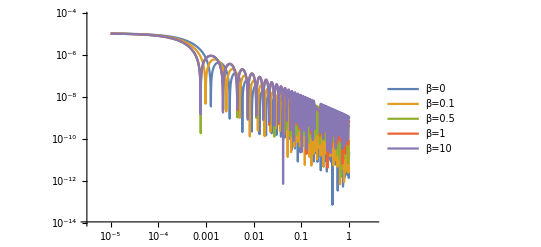

```mathematica
makePlot[haβ[1,β,1,0.01],{β,{0,0.1,0.5,1,10}}]
```

For larger β the curve converges to αM=0 at early times and deviates at late times.

### Varying αM0 for some β’s

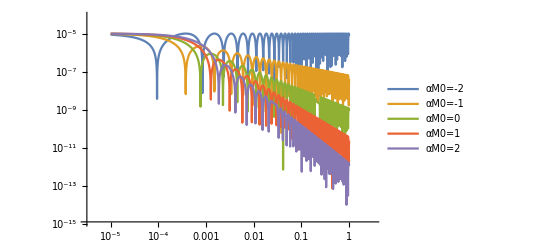
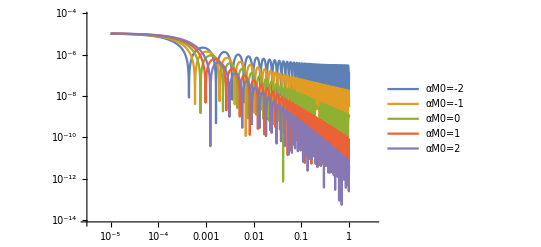
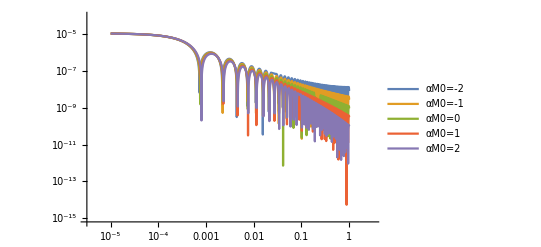
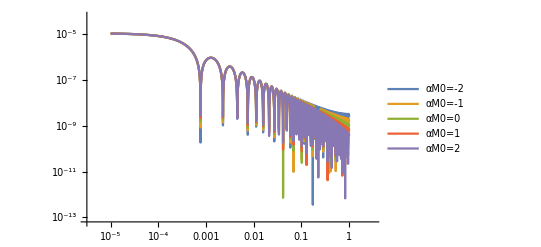

```mathematica
Table[makePlot[haβ[αM0,β,1,0.01],{αM0,{-2,-1,0,1,2}},SaveFilePrefix->"varying_aM0_beta_"<>TextString[β]],{β,{0,0.1,0.4,1}}]
```

## Slope of the Amplitude

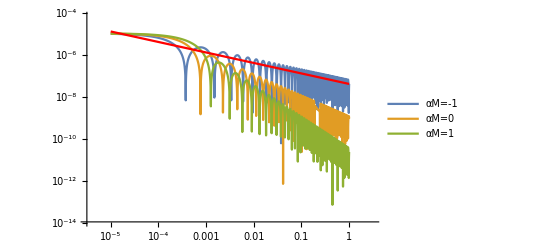

```mathematica
hSlope[a_][αM_]:=a^(-1-αM/2);
Show[makePlot[ha[0.01,1,αM],{αM,-1,1,1}],LogLogPlot[Evaluate[Table[hSlope[a][αM]*ha[0.01,1,αM][1],{αM,-1,1,1}]],{a,10^-5,1},PlotStyle->Directive[Thick,Red]]]
```

### Growing amplitude for αM<-2

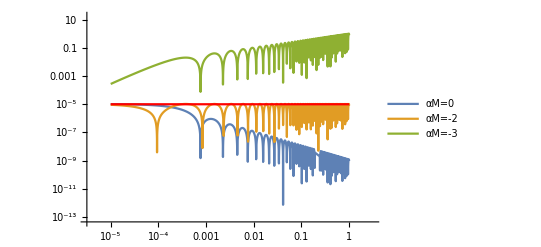

```mathematica
Show[makePlot[ha[0.01,1,αM],{αM,{0,-2,-3}},SaveFilePrefix->"growing_aM"],LogLogPlot[hSlope[a][-2]*10^(-5),{a,10^-5,1},PlotStyle->Directive[Thick,Red]]]
```

### de Sitter space

```mathematica
(*aInitial=10^-10;
aη[η_]:=η^-1
HconfdS[x_]:=L*(1-L*η)
sol=ParametricNDSolve[{h''[x]+(Hconf'[x]/Hconf[x]+2+αM)*h'[x]+(cT*k/Hconf[x])^2*h[x]==0,h[Log[aInitial]]==1,h'[Log[aInitial]]==0},h,{x,Log[aInitial],0},{k,cT,αM}];
ha[k_,cT_,αM_][a_]=hA[k]*h[k,cT,αM][x]/.sol/.x->Log[a];*)
```

## 2-metric coupling

```mathematica
eqg=hg''[x]+(Hconf'[x]/Hconf[x]+2+αMg)*hg'[x]+(mg^2+cTg*k/Hconf[x])^2*hg[x];
eqf=hf''[x]+(Hconf'[x]/Hconf[x]+2+αMf)*hf'[x]+(mf^2+cTf*k/Hconf[x])^2*hf[x];
sol=ParametricNDSolve[{eqg==qg*hf[x],eqf==qf*hg[x],hg[Log[aInitial]]==1,hg'[Log[aInitial]]==0,hf[Log[aInitial]]==1,hf'[Log[aInitial]]==0},{hg,hf},{x,Log[aInitial],0},{αMg,αMf,cTg,cTf,k,mg,mf,qg,qf}];
hga[αMg_,αMf_,cTg_,cTf_,k_,mg_,mf_,qg_,qf_][a_]=hA[k]*hg[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][x]/.sol/.x->Log[a];
hfa[αMg_,αMf_,cTg_,cTf_,k_,mg_,mf_,qg_,qf_][a_]=hA[k]*hf[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][x]/.sol/.x->Log[a];
(*params={αMg->0,αMf->-4,cTg->1,cTf->1,k->0.01,mg->10^-12,mf->0,qg->10^-12,qf->0}*)
```

{αMg→0,αMf→0,cTg→1,cTf→1,k→0.01,mg→0.8,mf→0,qg→0,qf→0}

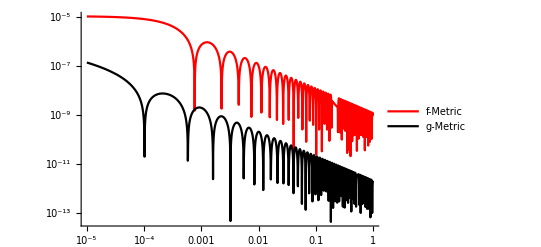

```mathematica
Options[makeBimetricPlot]={SaveFilePrefix->Null};
makeBimetricPlot[params_,OptionsPattern[]]:=(
Print[params];
If[Not[OptionValue[SaveFilePrefix]===Null]&&Not[preventSave],
datag=Table[{x,Log10[Abs[hga[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][10^x]/.params]]},{x,-5,0,0.001}];
Export[OptionValue[SaveFilePrefix]<>"_g"<>".csv",datag];
dataf=Table[{x,Log10[Abs[hfa[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][10^x]/.params]]},{x,-5,0,0.001}];
Export[OptionValue[SaveFilePrefix]<>"_f"<>".csv",dataf];
];
Show[
LogLogPlot[Abs[hfa[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][a]/.params],{a,10^-5,1},PlotLegends->Placed[{"f-Metric"},Right],PlotStyle->Red],
LogLogPlot[Abs[hga[αMg,αMf,cTg,cTf,k,mg,mf,qg,qf][a]/.params],{a,10^-5,1},PlotLegends->Placed[{"g-Metric"},Right],PlotStyle->Black],
PlotRange->Automatic
]
)
makeBimetricPlot[{αMg->0,αMf->0,cTg->1,cTf->1,k->0.01,mg->0.8,mf->0,qg->0,qf->0}]
```

{αMg→0,-1→-1,cTg→1,cTf→1,k→0.01,mg→0,mf→0,qg→1,qf→0}

{αMg→0,-2→-2,cTg→1,cTf→1,k→0.01,mg→0,mf→0,qg→1,qf→0}

{αMg→0,-3→-3,cTg→1,cTf→1,k→0.01,mg→0,mf→0,qg→1,qf→0}

{αMg→0,-4→-4,cTg→1,cTf→1,k→0.01,mg→0,mf→0,qg→1,qf→0}

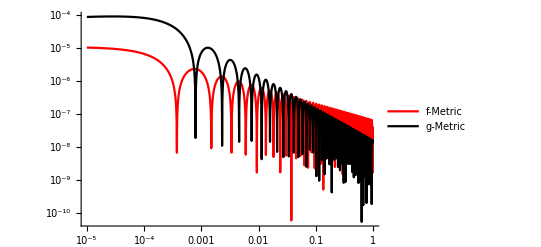
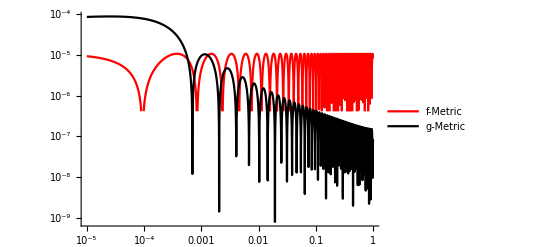
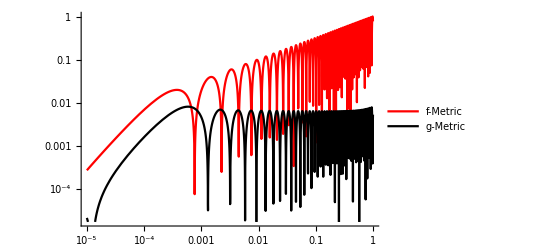
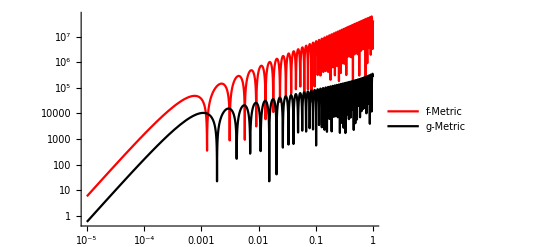

```mathematica
Table[makeBimetricPlot[{αMg->0,αMf->αMf,cTg->1,cTf->1,k->0.01,mg->0,mf->0,qg->1,qf->0},SaveFilePrefix->StringJoin["bimetric_aMf_",TextString[αMf]]],{αMf,{-1,-2,-3,-4}}]
```

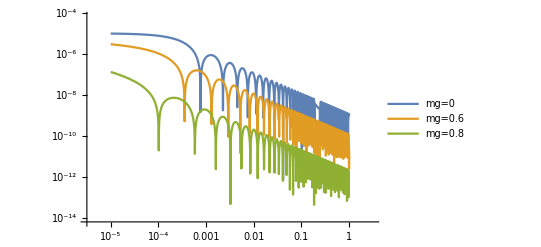

```mathematica
makePlot[hga[0,0,1,1,0.01,mg,0,0,0],{mg,{0,0.6,0.8}},SaveFilePrefix->"varying_mg"]
```

```mathematica
hgslope[αM_][a_]:=a^(-1-αM/2)+a^(-1-αM/2+2);
```

{αMg→0,αMf→-3,cTg→1,cTf→1,k→0.01,mg→0,mf→0,qg→1,qf→0}

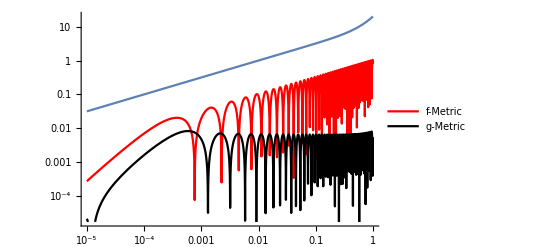

```mathematica
Show[makeBimetricPlot[{αMg->0,αMf->-3,cTg->1,cTf->1,k->0.01,mg->0,mf->0,qg->1,qf->0}],LogLogPlot[hgslope[-3][a]*10^(1),{a,10^-5,1}]]
```